# Dimensionnement d’un réacteur TBR de production de CH4 par une solution carbonate/bicarbonate.

```mathematica
Off[Solve::ifun]
(*température ambiante en K*)
Tn=313.15; 

(*J/(mol*K), la constante des gaz parfait*)
Rgp= 8.314;

(*Pression in en Pa*)
Pin=300000; 

(*Perte de charge linéique maximale recommandée en Pa/m*)
PPmax=205;

(*accélération de gravité m/s.b2*)
g= 9.81; 

(*masse volumique du liquide à l'entrée de la colonne kg/m.b3*)
ρl= 1030.5 ;

(*masse volumique du gas à l'entrée de la colonne en kg/m.b3*)
ρgas=3.50; 

(* Masse volumique de l'eau pure kg/m^3 *)
ρw = 992.2;

(* Viscosité dynamique du liquide à son entrée dans la colonne Pa.s*)
μl = 1.95*10^-3; 

(* Viscosité dynamique de l'eau pure Pa.s*)
μw = 0.653*10^-3; 

(* Viscosité dynamique du gaz à son entrée dans la colonne Pa.s*)
μg = 59.42*10^-6; 

(* Tension de surface  mN/m*)
σ = 69.6*10^-3; 

(* Tension de surface critique mN/m *)
σc = 61*10^-3; 

(*masse de MEA dans la solution liquide*)
α=0.3; 

(* Diamètre nominal d'un élément m*)
dp = 0.025; 

(* Porosité du garnissage *)
ε = 0.74;

(* Nombre d'éléments par unité de volume de la colonne dm^-3*)
Nbr = 85; 

(* Facteur d'empilement m^-1*)
Fp = 320; 
 
(*Débit gazeux nominal entrant Nm.b3/s*)
QNgin= 50000/3600;

(*Aire de la surface d'un élément par unité de volume de l'appareil en m^-1*)
Ap=250;

 (*constante de solubilité du CO2*)
hCO2=1.5 10^(-5) Tn Exp[1375/Tn];

(*Coefficient de diffusion de la MEA en phase liquide en m.b2/s*)
DMEA= Exp[-15-2200/Tn];

(*coefficient de diffusion du CO2 en phase liquide en m.b2/s*)
DCO2l=3 10^(-5)*Exp[-3096/Tn];

(*coefficient de diffusion du CO2 en phase gazeuse en m.b2/s*)
DCO2g=6.55 10^(-8)*Sqrt[Tn] ;

(*Coef stock de la réaction*)
ν2=2;

(*Constante cinétique de réaction du CO2 avec RNH2*)
κ= 10^(7.9-(2152/Tn));
```

## Objectif de la colonne

```mathematica
(*Fraction molaire sortant de la colonne imposée*)
yCO2out= 5*10^-5;

(*taux de charge dans le liquide pauvre*)
θin=0.1; 

(*taux de charge en sortie de colonne à garnissage*)
θout= 0.3;

(*Theta est le nombre de mol de CO2 dissous par mole de MEA en solution*)
```

## Calcul des masses molaires

```mathematica
yCO2in=0.193;
yN2in=0.7167;
yH2Oin=0.0811;
yArin=0.0092;
MMCO2=44 10^-3;
MMN2=28 10^-3;
MMH2O=18 10^-3;
MMAr=40 10^-3;

(*masse molaire de la monoéthanolamine g/mol*)
MMMEA=61 10^-3;

(*Masse molaire du gas à l'entrée g/mol*)
MMgin = yCO2in MMCO2+yN2in MMN2+yH2Oin MMH2O+yArin MMAr;(*yCO2in+yN2in+yArin+yH2Oin*)

(*Masse molaire du gaz inerte g/mol*)
MMInerte = (yN2in MMN2 + yH2Oin MMH2O + yArin MMAr)/(yN2in+yArin+yH2Oin) (*yN2in + yH2Oin + yArin*)
```

0.0271318

## Calcul des du débit de liquide entrant, la fraction massique et concentration

```mathematica
(*Pression (Pa) et Température (K) dans les conditions normales --> permet de calculer le volume molaire*)
PN=101325;
TN=273.15;
(*Débit entrant dans la colonne en kg/s*)
QGinKG =(QNgin PN)/(Rgp TN) MMgin;
(*Débit entrant en m3/s, grâce à une conversion*)
QGin=QGinKG/ρgas;

(*fraction massique de CO2 initialement dans le gas*)
xCO2in=(yCO2in MMCO2)/(yCO2in MMCO2 + (1-yCO2in) MMInerte);

(*fraction massique de CO2 imposé en sortie de colonne dans le gas*)
xCO2out=(yCO2out MMCO2)/(yCO2out MMCO2 + (1-yCO2out) MMInerte);

(*Qgout est le débit à la sortie de la colonne *)
QGoutKG = QGinKG (1-xCO2in)/(1-xCO2out);

(*Débit massique global d'absorption de CO2 en kg/s*)
TCO2 = QGinKG-QGoutKG;
 
(*Concentraion in et out en réactant, sachant la stochiométrie de la réaction *)
CMEAin=(α (1-2 θin))/(1+(α θin MMCO2/MMMEA));
CMEAout= (α (1-2 θout))/(1+(α θout MMCO2/MMMEA)) ;

(*Concentration in et out en fraction massique de CO2 dissous (kgCO2/kgliquide) sous forme de carbamate dans le liquide*)
CcarboneIN = (α θin MMCO2/MMMEA)/(1+(α θin MMCO2/MMMEA));

CcarboneOUT = (α θout MMCO2/MMMEA)/(1+(α θout MMCO2/MMMEA));

(*Débit liquide nécessaire pour absorber la quantité demandée de CO2*)
QLinKG = TCO2 (1-CcarboneOUT)/(CcarboneOUT-CcarboneIN);

(*Débit liquide en m.b3/s*)
QLin = QLinKG/ρl;
```

## Calcul du diamètre de la colonne

```mathematica
(*Vrai débit de liquide sortant de la colonne en kg/sec*)
QLout = QLin+TCO2/ρl;
(*Débit liquide sortant de la colonne en kg/s*)
QLoutKG = QLinKG + TCO2;


(* Relaton π2 *)
π2 = QLin/QGin √(ρl/ρgas);
(* Calcul de π1e *)
π1e = Exp[0.1117 - 4.012 π2^0.25];

(*Calcul de la vitesse superficielle à l'egorgement*)
Vsge = √(π1e/(Fp/g*ρgas/ρl*ρw/ρl*(μl/μw)^0.2));

(* Calcul des coefficients A1 et A2 *)
A1 = 21.79 - 36.19 π2^0.25 + 16.60 π2^0.5;
A2 = 7.06 + 10.30 π2^0.25 - 10.36 π2^0.5;

(* Équation quadratique pour x =π1/π1e *)
f[x] = 98 A2 (x)^2+98 A1 (x) - PPmax;
(* Racine positive de l'équation quadratique *)
sol = Solve[f[x] == 0, x];
x1= x/. sol[[2]];

(*x11= (-49 A1 +√((49 A1)^2+98 A2 205))/(98 A2)*)
(*Vitesse superficielle du gaz en réécrivant l'équation (Vsg/Vsg,e).b2= pi1/pi1,e, ou Vsg est en m/s*)
Vsg= Vsge √x1;

(*Calcul de la section de la colonne en m.b2*)
Ω=QGin/Vsg;

(*Diamètre de la colonne en m*)
Dcolonne = √((4 Ω)/Pi) (*Dreal = 4.481m;*);
```

## Détermination de la hauteur de la colonne permettant d’ateindre les conditions souhaitées en CO2

(* Evolution du débit de gas QG(z)*)
 QG'[z] == -tCO2[z];

(* Evolution de la fraction massique de CO2 dans la phase gazeuse *)
 xCO2'[z] == -((tCO2[z]) (1 - xCO2[z]))/QG[z];

(* Evolution du débit de liquide QL(z) *)
QL'[z] == tCO2[z];

(*Evolution de la concentration en MEA dans la phase liquide *)
CMEA'[z] ==tCO2[z]/((QL[z]) (2 MMMEA/MMCO2 + CMEA[z]));

### Détermination de TCO2(z)

```mathematica
(*Débit en m3/s*)
Vsl= QLin/Ω;
Aa=Ap*(1-Exp[-1.45 (σc/σ )^0.75 ((Vsl ρl)/(μl*Ap))^0.1 ((Vsl^2 ρl)/(σ Ap))^0.2 ((Vsl^2 Ap)/g)^-0.05]);
Print["Densité d'air interfaciale: ",Aa," m.b2 interface/m.b3 lit"]
(*fCO2[z] est exprimé en mol par sec par m.b2 (surface échange gas-liquide)*)
fCO2[z]= KGL[z]*P[z]/(Rgp Tn)*yCO2g[z];

(*Expression de la pression*)
P[z]=Pin-PPmax*z;

(*Expression de la fraction molaire de CO2 dans le gaz *)
yCO2g[z]=((xCO2[z]/MMCO2)/(xCO2[z]/MMCO2+(1-xCO2[z])/MMCO2));

(*Expression du coefficient de transfert gaz-liquide global*)
KGL[z]=(hCO2*Ee[z]*kG*kL)/(kG+hCO2*Ee[z]*kL);

(*coefficient de transfert en phase liquide m/s*)
kL=(Ap DCO2l) 0.0051 (Ap dp)^0.4 ((Vsl ρl)/(μl Ap))^1.33 (μl/(ρl DCO2l))^0.5 ((Vsl^2 Ap)/g)^-0.33 (*m/s*);
Print["Coefficient transfer en phase liquide: ",kL," m/s"]
(*coefficient de tranfert en phase gazeuse m/s*)
kG=  5.23*Ap*DCO2g*(Ap dp)^-2 ((Vsg ρgas)/(μg Ap))^0.7*(μg/(ρgas DCO2g))^0.5;
Print["Coefficient transert en phase gazuse: ",kG," m/s"]
(*Expression du facteur d'accélération Ee[z]*)
Ee[z]=1+Ha[z]/Ac[z] (1-Exp[-0.65 Ha[z] √Ac[z]]);

(*Le Hatta number s'exprime *)
Ha[z]=(√(κ*cMEA[z]*DCO2l))/kL;

(*Expression de Ac[z]*)
Ac[z]=Ha[z]/Nn[z]+Exp[0.68/Ha[z]-(0.45 Ha[z])/Nn[z]];

(*Expression de Nn[z]*)
Nn[z]=(DMEA cMEA[z])/(ν2 DCO2l hCO2 cCO2[z]);

(*La concentration en phase molaire en CO2 dans la phase gazeuse (en mol/m.b3)*)
cCO2[z]=P[z]/(Rgp Tn) yCO2g[z];

(*La concentration molaire en MEA libre dans la phase liquide cMEA[z] (en mol/m.b3) se déduit de part sa fraction massique*)
cMEA[z]= (CMEA[z] ρl)/MMMEA;
```

Densité d'air interfaciale: 134.63 m.b2 interface/m.b3 lit

Coefficient transfer en phase liquide: 0.0000494355 m/s

Coefficient transert en phase gazuse: 0.00320048 m/s

Rep4=NDSolve[{CMEA'[z]=tCO2[z]/(QL[z]) ((2 MMMEA)/MMCO2+CMEA[z]),CMEA'[0]==CMEAin},CMEA[z],{z,0,2}]
Rep3=NDSolve[{QL'[z]=-tCO2 [z],QL'[0]==QLin},QL[z],{z,0,2}]
Rep2=NDSolve[{QG'[z]=-tCO2 [z],QG'[0]==QNgin/3600},QG[z],{z,0,2}]
Rep1=NDSolve[{xCO2'[z]==-(tCO2[z] (1-xCO2[z]))/G[z], xCO2[0]==xCO2in},xCO2[z],{z,0,2}]

## Résolution des équations différentielles

{QG[0]==18.8307,xCO2[0]==0.279458,QL[0]==129.46,CMEA[0]==0.112685}

La taille de la colonne est 10.8136

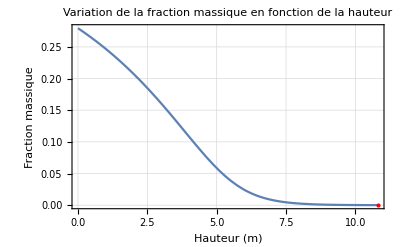

```mathematica
ConditionInitial={QG[0]== QGinKG, xCO2[0]==xCO2in, QL[0]==QLoutKG, CMEA[0]==CMEAout}
(*tCO2[z] est exprimé en nombre de kg de CO2 transférées par unité de temps et par unité de hauteur de la colonne*)
tCO2[z]=Aa Ω MMCO2 fCO2[z];
sol=NDSolve[Join[{ QG'[z] == -tCO2[z], xCO2'[z] == -(tCO2[z] (1 - xCO2[z]))/QG[z], QL'[z] == tCO2[z], CMEA'[z] ==tCO2[z]/QL[z] ((2 MMMEA)/MMCO2+ CMEA[z])},ConditionInitial,{WhenEvent[xCO2[z]==xCO2out,{height=z, Print["La taille de la colonne est ", z];"StopIntegration"}]}], {QG[z], xCO2[z], QL[z], CMEA[z]}, {z,0,30} ][[1]];

(* Ajout d'un point à la valeur de xCO2out *)
Show[Plot[xCO2[z] /. sol, {z, 0, (height /. sol)}, 
  PlotLabel -> "Variation de la fraction massique en fonction de la hauteur", 
  AxesLabel -> {"Hauteur (m)", "Fraction massique"},
  Frame -> True, 
  FrameStyle -> Directive[Thick, Black], 
  GridLines -> Automatic],
  Graphics[{PointSize[Medium], Red, Point[{(height /. sol), xCO2out}]}]]
```